```mathematica
(* GRAPH *)
```

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
SetDirectory@NotebookDirectory[];
<<MaTeX`
```

```mathematica
<<ErrorBarPlots`
```

```mathematica
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,nicefrac,esint,siunitx,bm,ctex}"},"Magnification"->1.5];
MyTeX[x_]:=HideText[MaTeX[x]];
HideText["* Some Basic setup *"]
```

* Some Basic setup *

```mathematica
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\xelatex.exe"];*)
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\pdflatex.exe"];*)
HideText["* Engine unchanged, possibly pdfLaTeX *"]
```

* Engine unchanged, possibly pdfLaTeX *

```mathematica
omarker=Graphics[{Thickness[.2],Disk[]}];
```

```mathematica
(rawData=Import["data0.xlsx"]⟦1⟧⟦1;;,{1,2,5,6}⟧)//TableForm;
dataWithError=Join[{#}&/@rawData⟦2;;-1,{2,3}⟧,Map[ErrorBar,rawData⟦2;;-1,{4}⟧,{2}],2];
dataTrend=rawData⟦All,{2,3}⟧;
```

```mathematica
frame={
MaTeX["I / \\si{\\mA}",Magnification->.8],
MaTeX["R / \\si{\\uW}",Magnification->.8]};
```

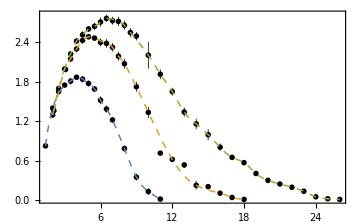

plotPowerAmp1.pdf

```mathematica
plotPowerAmp1=Show[{
ErrorListPlot[dataWithError⟦1;;70⟧,
PlotTheme->"Scientific",
ImageSize->Medium,
ImageMargins->{{0,40},{0,0}},
GridLines->None,
FrameLabel->frame,
PlotMarkers->{omarker,.012},
PlotStyle->Directive[Thickness[.0015],Black]],
ListLinePlot[{
dataTrend⟦2;;16⟧,
Select[dataTrend⟦17;;39⟧,!MemberQ[dataTrend⟦{25,32,34,36},1⟧,#⟦1⟧]&],
Select[dataTrend⟦40;;71⟧,!MemberQ[dataTrend⟦{50,54},1⟧,#⟦1⟧]&]
},
PlotStyle->Directive[Thickness[.003],Dashed],
InterpolationOrder->3,
PlotLegends->Placed[(MaTeX[#,Magnification->.8]&/@{
"\\SI{641}{\\Pa}",
"\\SI{513}{\\Pa}",
"\\SI{481}{\\Pa}"
}),{{.7,0.5},{0,0}}]]
},PlotRange->All];
Magnify[%,1.5]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@plotPowerAmp1
```

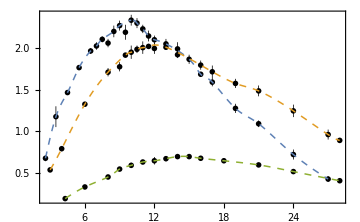

plotPowerAmp2.pdf

```mathematica
plotPowerAmp2=Show[{
ErrorListPlot[dataWithError⟦71;;130⟧,
PlotTheme->"Scientific",
ImageSize->Medium,
ImageMargins->{{0,40},{0,0}},
GridLines->None,
FrameLabel->frame,
PlotMarkers->{omarker,.012},
PlotStyle->Directive[Thickness[.0015],Black]],
ListLinePlot[{
Select[dataTrend⟦72;;96⟧,!MemberQ[dataTrend⟦{79,82,89},1⟧,#⟦1⟧]&],
Select[dataTrend⟦97;;116⟧,!MemberQ[dataTrend⟦{101,107,109},1⟧,#⟦1⟧]&],
Select[dataTrend⟦117;;131⟧,!MemberQ[dataTrend⟦{},1⟧,#⟦1⟧]&]
},
PlotStyle->Directive[Thickness[.003],Dashed],
InterpolationOrder->3,
PlotLegends->Placed[(MaTeX[#,Magnification->.8]&/@{
"\\SI{374}{\\Pa}",
"\\SI{299}{\\Pa}",
"\\SI{235}{\\Pa}"
}),{{.72,0.56},{0,0}}]]
},PlotRange->All];
Magnify[%,1.5]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@plotPowerAmp2
```

```mathematica
plotPowerAmpAll=ListLinePlot[{
dataTrend⟦2;;16⟧,
Select[dataTrend⟦17;;39⟧,!MemberQ[dataTrend⟦{25,32,34,36},1⟧,#⟦1⟧]&],
Select[dataTrend⟦40;;71⟧,!MemberQ[dataTrend⟦{50,54},1⟧,#⟦1⟧]&],
Select[dataTrend⟦72;;96⟧,!MemberQ[dataTrend⟦{79,82,89},1⟧,#⟦1⟧]&],
Select[dataTrend⟦97;;116⟧,!MemberQ[dataTrend⟦{101,107,109},1⟧,#⟦1⟧]&],
Select[dataTrend⟦117;;131⟧,!MemberQ[dataTrend⟦{},1⟧,#⟦1⟧]&]
},
PlotTheme->"Scientific",
ImageSize->Medium,
ImageMargins->{{15,0},{0,0}},
GridLines->None,
FrameLabel->frame,
PlotStyle->Directive[Thickness[.003]],
InterpolationOrder->3,
PlotLegends->Placed[(MaTeX[#,Magnification->.8]&/@{
"\\SI{641}{\\Pa}",
"\\SI{513}{\\Pa}",
"\\SI{481}{\\Pa}",
"\\SI{374}{\\Pa}",
"\\SI{299}{\\Pa}",
"\\SI{235}{\\Pa}"
}),{{1.03,0.16},{0,0}}],
PlotRange->All];
Magnify[%,1.5]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@plotPowerAmpAll
```

-Graphics-

plotPowerAmpAll.pdf

```mathematica
SystemOpen["plotPowerAmpAll.pdf"]
```